```mathematica
SetDirectory["N:\\0MPX\\num300\\num300B"];   
<<param\\paramCertain; (* certain param *)
<<param\\paramUncertSelected73BCD;    (* matrix with sets of values for uncert param *)
```

```mathematica
Print["nSel=number param combinations selected from fitting to days 1-73 = ",nSel];
Print["Kpar1=number uncert param in May (without changes) = ",Kpar];
CTrepetions=20; (* repetitions of selected CT_param *)
nNew=nSel*CTrepetions;
Print["nNew=number param combinations with changes = ",nNew];
```

nSel=number param combinations selected from fitting to days 1-73 = 216

Kpar1=number uncert param in May (without changes) = 22

nNew=number param combinations with changes = 4320

```mathematica
(*---------------------------------------------------------*)
(* GENERATE UNCERTAIN PARAM FOR changes *)
(*---------------------------------------------------------*)
numpar={    1 ,    2 ,     3,    4 ,    5,     6,       7,      8,          9,          10};
numpar={  13,     14,   15, 16,  17,    18,    19,     20 ,     21,        22};
UPN      ={tis2,tis3,t1,t2,cas2,cas3,cas4,casB2,casB3,casB4};  
Fmin=    {  2,         2 ,    52,70,  .0,    0,       0,         0,          0,        0};    
Fmax=    {  8,         8,     62,80,  .3,   .3,     .3,      .3,        .3,     .3};

NGpar=Length[Fmin];

(* create array *)
nmaxsim2=nNew;
up2Mat=Array[up2,{nmaxsim2,NGpar}];
xx=Range[nmaxsim2];
Do[increment=(Fmax[[j]]-Fmin[[j]])/nmaxsim2;
correction=increment/10;
intervMin=Fmin[[j]]+(xx-1)*increment;
intervMax=Fmin[[j]]+xx*increment-correction;
randIndex=RandomSample[Range[nmaxsim2]];    (* PermutationList[RandomPermutation[nmaxsim]];*)
Do[up2[i,j]=(intervMax[[randIndex[[i]]]]-intervMin[[randIndex[[i]]]])*RandomReal[]+intervMin[[randIndex[[i]]]],{i,1,nmaxsim2}],
{j,1,NGpar}];
```

```mathematica
Kpar1=Kpar-NGpar;
upNewMat=Array[upNew,{nNew,Kpar}];
Do[ Do[Do[upNew[(L-1)*nSel+ii,ipar]=upSel[ii,ipar],{ii,1,nSel}],{ipar,1,Kpar1}],{L,CTrepetions}];
        Do[Do[upNew[ii,ipar]=up2[ii,ipar-Kpar1],{ii,1,nNew}],                            {ipar,Kpar1+1,Kpar}];
```

```mathematica
(*----------------------------RUN ALL ----------------------------*)
Tmax=91;            (* #days to run *)
nsim=nNew;

(* initial conditions *) 
SUini=State0[[1]]; EUini=State0[[2]]; IUini=State0[[3]];YUini=State0[[4]];
SVini=State0[[5]]; EVini=State0[[6]]; IVini=State0[[7]];YVini=State0[[8]];
SPini=State0[[9]]; EPini=State0[[10]]; IPini=State0[[11]];YPini=State0[[12]];
RRini=State0[[13]]; HHini=State0[[14]]; 

(* total size of popul & infectious pop *)
Ntot[i_,t_]:=SU[i][t]+EU[i][t]+IU[i][t]+YU[i][t]+SV[i][t]+EV[i][t]+IV[i][t]+YV[i][t]+SP[i][t]+EP[i][t]+IP[i][t]+YP[i][t]+RR[i][t]+HH[i][t]; (*group i *)
Ntot[t_]:=Sum[Ntot[i,t],{i,1,ag}];    (* tot pop *)
Itot[t_]:=Sum[IU[i][t]+IV[i][t]+IP[i][t],{i,1,ag}];    (* total INFECTIOUS not-isolated *)
Ytot[t_]:=Sum[YU[i][t]+YV[i][t]+YP[i][t],{i,1,ag}];   (* total INFECTIOUS isolated *)
```

```mathematica
(*--------- VACCINATION BEFORE 25JULY2022 (CONTACTS OF CASES) ------------------*)
phi1d    =Izero;  (* vaccination of uninfected *)
phi2d    =Izero; (* vaccination of exposed *)
XTvac[t_]:=Piecewise[{{0,  t<42}, (* first 4w  *)
                                               {vacRate1,42≤t   }    }]
```

```mathematica
(*------------CHANGES IN JUNE/JULY ------------------------------------------*)
t1=57;t2=75;
casF4[t_]    :=Piecewise[{{0,t<t2},{cas4,t2≤t }}] ;
casF3[t_]    :=Piecewise[{{0,t<t2},{cas3,t2≤t }}] ;
casF2[t_]    :=Piecewise[{{0,t<t2},{cas2,t2≤t }}] ;

rateTOisolF[t_]  :=Piecewise[{{1/Tisol1,                                          t<t2},{1/Tisol3,t2≤t }}] ;
rateOUTisolF[t_]:=Piecewise[{{1/(infectiousDays-Tisol1),t<t2},{1/(infectiousDays-Tisol3),t2≤t }}] ;
```

```mathematica
(************* LOOP ************)
Do[ (* START of loop of runs for each param set *)
t1=upNew[j,15];
t2=upNew[j,16];

theta             =1/upNew[j,1];
infectiousDays=upNew[j,2];  
Tisol1                  =upNew[j,12];
Tisol2                  =upNew[j,13];
Tisol3                  =upNew[j,14];delta=rateTOisolF[t];gamma=rateOUTisolF[t];  

betaS=upNew[j,3];
aC4   =upNew[j,4];aCbef={aCd[[1]],aCd[[2]],aCd[[3]],aC4};
cas2=upNew[j,17]; 
cas3=upNew[j,18]; 
cas4=upNew[j,19];
casB2=upNew[j,20]; 
casB3=upNew[j,21]; 
casB4=upNew[j,22];aCcha={casF2[t],casF2[t],casF3[t],casF4[t]};aC=aCbef-aCbef*aCcha;

w                =upNew[j,5];
epsilonM=upNew[j,6];
epsilonC=upNew[j,7];
vacRate1=upNew[j,8];phi1={0,0,XTvac[t],XTvac[t]}; phi2=phi1;
v1             =upNew[j,9];sigma1=v1;sigma1HAT=v1;(* oldVE *)
v2             =upNew[j,10];sigma2=v2; (*newVE *)
zeta        =upNew[j,11];

(* parameters for transm prob with sex partners *) 
Bs[k_,l_]  :=(1-        betaS)^((uM[[k]]+uM[[l]])/2);(* sex contacts with main partn *)
Bsv[k_,l_]:=(1-v1*betaS)^((uM[[k]]+uM[[l]])/2);
Bsp[k_,l_]:=(1-v2*betaS)^((uM[[k]]+uM[[l]])/2);

(* mixing *)
mM[i_,l_,t_]:=epsilonM*dd[i][[l]]+(1-epsilonM)*aM[[l]]*Ntot[l,t]/Sum[aM[[jp]]*Ntot[jp,t],{jp,1,ag}];
mC[i_,l_,t_]:=epsilonC*dd[i][[l]]+(1-epsilonC)*aC[[l]]*Ntot[l,t]/Sum[aC[[jp]]*Ntot[jp,t],{jp,1,ag}];

(* LAMBDA'S *)
lambdaM[i_,t_ ]:=q[[i]]*Sum[ mM[i,l,t]*((1-Bs[i,l])*(IU[l][t]+w*YU[l][t])+(1-Bsv[i,l])*(IV[l][t]+w*YV[l][t])+(1-Bsp[i,l])*(IP[l][t]+w*YP[l][t]))/Ntot[l,t],{l,1,ag}];
lambdaC[i_,t_ ]:=aC[[i]]*betaS*Sum[ mC[i,l,t]*((IU[l][t]+w*YU[l][t])+v1*(IV[l][t]+w*YV[l][t])+v2*(IP[l][t]+w*YP[l][t]))/Ntot[l,t],{l,1,ag}];
lambda[i_,t_ ]     :=lambdaM[i,t ]+lambdaC[i,t ];

(* SOLVE  *)
xequa=Join[
Table[SU[i]'[t]  ==-(mu+lambda[i,t]+phi1[[i]])*SU[i][t]+mu*Ntot[i,t],{i,ag}],
Table[EU[i]'[t]==-(mu+phi2[[i]]+theta)*EU[i][t]+lambda[i,t]*SU[i][t],{i,ag}],
Table[IU[i]'[t]==-(mu+mud+delta+zeta)*IU[i][t]+theta*EU[i][t],{i,ag}],
Table[YU[i]'[t]==-(mu+mud+gamma+zeta)*YU[i][t]+delta*IU[i][t],{i,ag}],
Table[SV[i]'[t]==-(mu+sigma1*lambda[i,t]+phi1[[i]])*SV[i][t],{i,ag}],
Table[EV[i]'[t]==sigma1HAT*lambda[i,t]*SV[i][t]-(mu+theta+phi2[[i]])*EV[i][t],{i,ag}],
Table[IV[i]'[t]==sigma1*theta*EV[i][t]-(mu+mud+delta+zeta)*IV[i][t],{i,ag}],
Table[YV[i]'[t]==delta*IV[i][t]-(mu+mud+gamma+zeta)*YV[i][t],{i,ag}],
Table[SP[i]'[t]==phi1[[i]]*(SU[i][t]+SV[i][t])-(mu+sigma2*lambda[i,t])*SP[i][t],{i,ag}],
Table[EP[i]'[t]==sigma2*lambda[i,t]*SP[i][t]+phi2[[i]]*(EU[i][t]+EV[i][t])-(mu+theta)*EP[i][t],{i,ag}],
Table[IP[i]'[t]==sigma2*theta*EP[i][t]-(mu+delta)*IP[i][t],{i,ag}],
Table[YP[i]'[t]==delta*IP[i][t]-(mu+gamma)*YP[i][t],{i,ag}],
Table[RR[i]'[t]  ==-mu*RR[i][t]+(1-sigma1)*theta*EV[i][t]+(1-sigma2)*theta*EP[i][t]+gamma*(Ytot[t]+HH[i][t]),{i,ag}],
Table[HH[i]'[t]  ==-(mu+mud+gamma)*HH[i][t]+zeta*(IU[i][t]+YU[i][t]+IV[i][t]+YV[i][t]),{i,ag}],


Table[SU[i][0]==SUini[[i]],{i,ag}],
Table[EU[i][0]==EUini[[i]],{i,ag}],
Table[IU[i][0]==IUini[[i]],{i,ag}],
Table[YU[i][0]==YUini[[i]],{i,ag}],
Table[SV[i][0]==SVini[[i]],{i,ag}],
Table[EV[i][0]==EVini[[i]],{i,ag}],
Table[IV[i][0]==IVini[[i]],{i,ag}],
Table[YV[i][0]==YVini[[i]],{i,ag}],
Table[SP[i][0]==SPini[[i]],{i,ag}],
Table[EP[i][0]==EPini[[i]],{i,ag}],
Table[IP[i][0]==IPini[[i]],{i,ag}],
Table[YP[i][0]==YPini[[i]],{i,ag}],
Table[RR[i][0]==RRini[[i]],{i,ag}],
Table[HH[i][0]==HHini[[i]],{i,ag}]           ];
xvar=Join[Flatten[Table[{SU[i],EU[i],IU[i],YU[i],SV[i],EV[i],IV[i],YV[i],SP[i],EP[i],IP[i],YP[i],RR[i],HH[i]},{i,ag}]] ];
xresult=NDSolve[xequa,xvar,{t,0,Tmax},MaxSteps->50000];  

(* epidemic outcomes to keep from selected runs *)
nSympFUN[t_]             :=Sum[theta*(EU[i][t]+sigma1*EV[i][t]+sigma2*EP[i][t]),{i,1,ag}]; 
nSympEle[j]=(nSympFUN[t]/.xresult)[[1]];

If[Mod[j,200]==0 ,Print[j]],
 {j,1,nsim}];(* END of loop of runs for each param set *)
```

200

400

600

800

1000

1200

1400

1600

1800

2000

2200

2400

2600

2800

3000

3200

3400

3600

3800

4000

4200

```mathematica
(*----- time points ------*)
tpoint=Table[it,{it,0,Tmax,1}];ntpoints=Length[tpoint];

(*----- save number daily cases --------*)
nSympMat  =Array[nSymp,{ntpoints}];
Do[t=tpoint[[it]];
nSymp[it]=Table[Evaluate[nSympEle[js]],{js,nsim}];
cumSymp[it]=Sum[nSymp[kk],{kk,1,it}];
,{it,1,ntpoints}];
nsim
```

4320

```mathematica
(*----------- IMPORT DATA TO FIT  -------------------*)
dataAll=Flatten[Import["CasesPerOnsetDate.xls"]];
dataFit=Table[dataAll[[j]],{j,1,Tmax}];(* use onset dates 27042022 up to & including 25072022 *)
ndataFit=Length[dataFit]
```

91

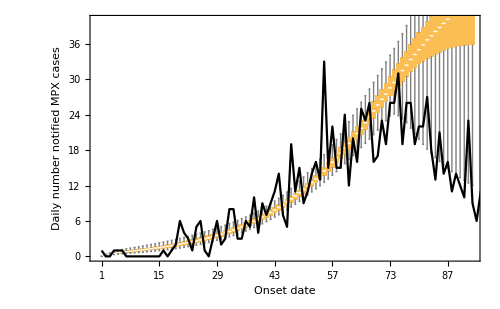

```mathematica
Show[ 
BoxWhiskerChart[Table[Table[nSymp[it+0][[j]], {j,nsim}],{it,Tmax-0}],PlotRange->{{0,Tmax},{0,40}},BaseStyle->{FontFamily->"Arial",FontSize->12},
ChartLabels->{"1","","","","","","","8","","","","","","","15","","","","","","","22","","","","","","","29","","","","","","","36","","","","","","","43","","","","","","","50","","","","","","","57","","","","","","","64","","","","","","","73","","","","","","","80","","","","","","","87","","","","","","","94","","","","","","","101"},Frame->{True,True,False,False},FrameLabel->{"Onset date","Daily number notified MPX cases"}],
ListPlot[Table[{it,dataAll[[it+0]]},{it,1,Length[dataAll]-0}],PlotStyle->{Black},Joined->True],
ImageSize->500]
```

```mathematica
(************************************************************)
(* new selection with changes *)
(************************************************************)
```

```mathematica
(* define matrices to save results*)
upSelBMat  =Array[upSelB,{nsim,Kpar}];
xSelBMat    =Array[xSelB,  {nsim}];
rSelBMat    =Array[rSelB,  {nsim}];

(* likelihoods & selection *)
pl=Table[Product[nSymp[k][[j]]^dataFit[[k]]*Exp[-nSymp[k][[j]]]/Factorial[dataFit[[k]]],{k,73,91}], {j,1,nsim}] ;(* Poisson Likelihood *) 
cw=Table[Sum[pl[[js]],{js,1,j}], {j,1,nsim}]/Sum[pl[[jk]],{jk,1,nsim}];(* cumulative weights: w1, w1+w2, ..., w1+w2+...+wNSIM *)
U=RandomReal[1,nsim]; (* sample nsim values from U(0,1) distribution *) 

(* Count how many of the U(0,1) values sampled are in each interval (CumW[k],CumW[k+1])  *)
cc[1]=Count[U,u_/;u<=cw[[1]]];
Do[cc[k]=Count[U,u_/;cw[[k-1]]<u<=cw[[k]]]
,{k,2,nsim}];

nSelB=0;  
Do[     
If[cc[j]>0 ,
(*THEN*) nSelB=nSelB+1;xSelB[j]=1;rSelB[nSelB]=cc[j];Do[upSelB[nSelB,ipar]=upNew[j,ipar],{ipar,1,Kpar}]  ,
(*ELSE*) xSelB[j]=0], (* close If *)
{j,nsim}]; (* close Do *)
s1=Select[Range[nsim],xSelB[#]==0&];
s2=Select[Range[nsim],xSelB[#]== 1&];
indexSelB=s2;
Print["Number of par sets selected = ", nSelB] (* was 438 *)
nmaxsimB=Sum[rSelB[j],{j,nSelB}]
```

Number of par sets selected = 16

4320

```mathematica
Table[rSelB[j],{j,nSelB}]
```

{10,478,1,2,239,1084,2,1,14,8,226,4,646,1,541,1063}

```mathematica
(*********************************************************************)
Save["param\\paramUncSELB",  {rSelB,xSelB,nSelB,indexSelB,nmaxsimB,upSelBMat,UPName,Kpar,Tmax,dataFit,ndataFit,dataAll}]
(*********************************************************************)
```

```mathematica
Do[t=tpoint[[it]];
nSympAll[it]=Flatten[Table[Table[nSymp[it][[s2[[j]]]],rSelG[j]] ,{j,nSelG}]];
cumSympAll[it]=Sum[nSympAll[kk],{kk,1,it}];
,{it,1,ntpoints}]
```

Table::iterb: Iterator {j,nSelG} does not have appropriate bounds.

Table::iterb: Iterator {rSelG[j]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.